```mathematica
explicitSum[f_,stepsize_,d_]:=stepsize^d Sum[f@@(x/@Range[d]),##]&@@Sequence[Table[{x[i],0,1,stepsize},{i,1,d}]]

totalSum[f_,stepsize_,d_]:=stepsize^d findSum[f,stepsize,d]
```

```mathematica
coeffs=fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{3,3}];
```

```mathematica
Sqrt[0.005^2 Sum[(Sin[Pi i+j]-fullReconstruct[coeffs,{i,j}])^2,{i,0,1,.005},{j,0,1,.005}]]
```

0.0107815

```mathematica
Timing[Sqrt[0.005^2 Sum[(Sin[Pi i+j]-fullReconstruct[coeffs,{i,j}])^2,{i,0,1,.005},{j,0,1,.005}]]]
```

{171.407,0.0107815}

```mathematica
Table[Sqrt[0.05^2 Sum[(Sin[Pi i+j]-fullReconstruct[#,{i,j}])^2,{i,0,1,.05},{j,0,1,.05}]&@fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{n,n}]],{n,1,5}]
```

```mathematica
fullError={0.16428309358579668,0.04311824666968759,0.010922142274398607,0.0027395147070991195,0.0006854411527070881}
```

{0.164283,0.0431182,0.0109221,0.00273951,0.000685441}

```mathematica
sparseError=Table[Sqrt[0.05^2 Sum[(Sin[Pi i+j]-fullReconstruct[#,{i,j}])^2,{i,0,1,.05},{j,0,1,.05}]&@sparseCoefficients[Sin[Pi #[[1]]+#[[2]]]&,n,2]],{n,1,7}]
```

{0.15943,0.106909,0.0340714,0.0106635,0.00322183,0.000956049,0.00027648}

```mathematica
fullLengths=Table[fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{n,n}]//Length,{n,1,5}]
```

{9,25,81,289,1089}

```mathematica
sparseLengths=Table[sparseCoefficients[Sin[Pi #[[1]]+#[[2]]]&,n,2]//Length,{n,1,7}]
```

{6,12,25,53,113,241,513}

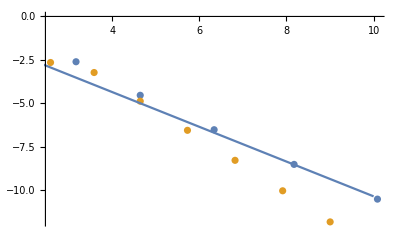

```mathematica
Show[ListPlot[{Table[{fullLengths[[i]],fullError[[i]]},{i,1,Length[fullError]}],Table[{sparseLengths[[i]],sparseError[[i]]},{i,1,Length[sparseError]}]}//Log2],Plot[-1 x-.35,{x,0,10}]]
```

```mathematica
Table[Sqrt[0.05^3 Sum[(Sin[Pi i+j+Pi k]-fullReconstruct[#,{i,j,k}])^2,{i,0,1,.05},{j,0,1,.05},{k,0,1,.05}]&@sparseCoefficients[Sin[Pi #[[1]]+#[[2]]+Pi#[[3]]]&,n,3]],{n,1,3}]
```

{1.15677,0.291658,0.360107}

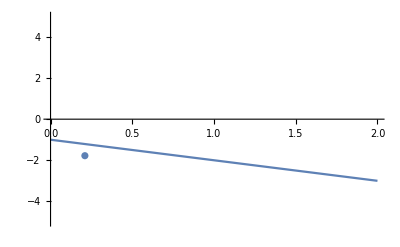

```mathematica
Show[Plot[-x-1,{x,0,2},PlotRange->5],ListPlot[{{0.27401112370472946,0.07750475000539797},{1.1567707982179598,0.29165751883293595}}//Log2]]
```

```mathematica
NIntegrate[(Sin[Pi x+y]-fullReconstruct[#,{i,j}])^2,{x,0,1},{y,0,1}]&@spCoefficients[Sin[Pi #[[1]]+#[[2]]]&]
```

```mathematica
{1.1567707982179598,0.29165751883293595}//Log2
```

{0.210103,-1.77765}

```mathematica
upperBound[stepsize_,x_]:=stepsize Floor[x/stepsize]
lowerBound[stepsize_,x_]:=stepsize Floor[x/stepsize]
construct[coeffs_,x_,n_]:=Module[{indices},indices=pointIndex[x,{n,n}];
Return[Sum[coeffs[[{k1+2,indices[[1,k1+2]],k2+2,indices[[2,k2+2]]}]] ϕ[{k1,k2},{indices[[1,k1+2]],indices[[2,k2+2]]}][#],{k1,-1,n},{k2,-1,n}]&
];
]
getSquare[f_,coeffs_,n_,X1_,X2_,stepsize_]:=Module[{g},g=construct[coeffs,{(X1+1/2)/2^(n-1),(X2+1/2)/2^(n-1)},n];Return[Sum[(f[{i,j}]-g[{i,j}])^2,{i,lowerBound[X1/2^(n-1),stepsize],upperBound[(X1+1)/2^(n-1),stepsize],stepsize},{j,lowerBound[X2/2^(n-1),stepsize],upperBound[(X2+1)/2^(n-1),stepsize],stepsize}]];]
getError2D[f_,n_,stepsize_]:=Module[{coeffs},coeffs=fullCoefficients[f,{n,n}];Return[Sum[getSquare[f,coeffs,n,X1,X2,stepsize],{X1,0,2^(n-1)},{X2,0,2^(n-1)}]//Sqrt];]
```